# Functional form harvest output vs preciptation

## Coefficient functions

```mathematica
ClearAll[x,a,b,y]
```

```mathematica
a = 17.29875+(1.540988-17.29875)/(1.003167+48.42166*Exp[-0.001624246*z])^(1/0.2041278)
```

17.2988-15.7578/((1.00317+48.4217 ⅇ^(-0.00162425 z))^4.89889)

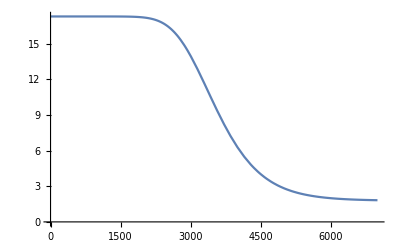

```mathematica
Plot[a,{z,0,7000}]
```

```mathematica
a = -0.0033245291416422705*z + 18.96521469
```

18.9652-0.00332453 z

```mathematica
b=-0.0001300155*z*Exp[-0.0003868268*z]
```

-0.000130016 ⅇ^(-0.000386827 z) z

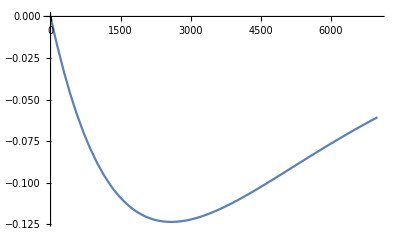

```mathematica
Plot[b,{z,0,7000}]
```

```mathematica
b = -0.01184748*Log[z]
```

-0.0118475 Log[z]

Where z is precipitation.

## Harvest Output function

```mathematica
y = a x Exp[b x]
```

ⅇ^(-0.000130016 ⅇ^(-0.000386827 z) x z) (17.2988-15.7578/((1.00317+48.4217 ⅇ^(-0.00162425 z))^4.89889)) x

## Plotting harvest output vs precipitation

```mathematica
Plot3D[y,{x,0,4},{z,0,7000}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
a/. {z-> 6000}
```

1.99626

```mathematica
b/.{z-> 6000}
```